```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0
```

Y^(0,1)[x,t]-𝒟 Y^(2,0)[x,t]==0

```mathematica
f0[t_]:=1-t
```

```mathematica
f1[t_]:=0
```

```mathematica
g0[x_]:=1-x
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→(-1+t) (-1+x)+((2-2 ⅇ^(-π^2 t 𝒟 K[1]^2)) Sin[π x K[1]])/(π^3 K[1]^3)K[1]1∞}}

```mathematica
Yf[x_,t_]:=Y[x,t]/.sol[[1]]
```

```mathematica
Yf[x_,t_,𝒟_]:=(-1+t) (-1+x)+∑_(k=1)^100 ((2-2 ⅇ^(-π^2 t 𝒟 k^2)) Sin[π x k])/(π^3 k^3)
```

```mathematica
d=1
```

1

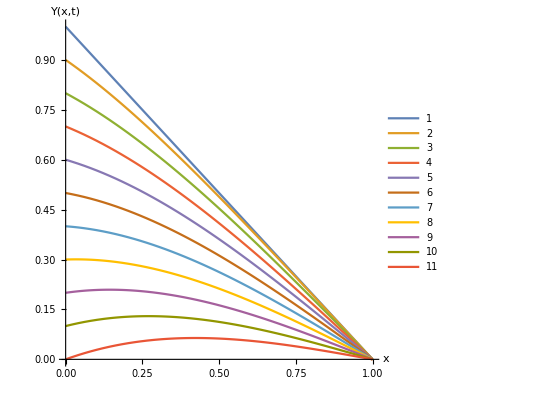

```mathematica
Plot[{Yf[x,0,d],Yf[x,0.1,d],Yf[x,0.2,d],Yf[x,0.3,d],Yf[x,0.4,d],Yf[x,0.5,d],Yf[x,0.6,d],Yf[x,0.7,d],Yf[x,0.8,d],Yf[x,0.9,d],Yf[x,1.0,d]},{x,0,1},PlotRange->{0,1},AxesLabel->{"x","Y(x,t)"},PlotLegends->Automatic,AspectRatio->1]
```